# Circuit diagram and graph

Visualize quantum circuits

## Example Content

In the Wolfram quantum framework, one can use the rich visualization functionalities of Wolfram Language, to create circuit diagrams and graphs.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Show the diagram of a quantum circuit:

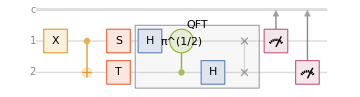

```mathematica
QuantumCircuitOperator[{"X","CNOT","T"->2,"S","Fourier",{1},{2}}]["Diagram"]
```

Visualize the corresponding topology of a circuit:

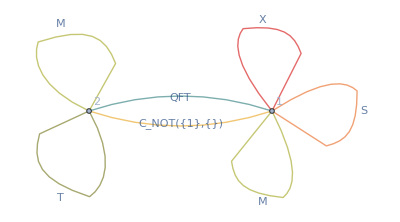

```mathematica
QuantumCircuitOperator[{"X","CNOT","T"->2,"S","Fourier",{1},{2}}]["Topology",EdgeLabels->Automatic]
```

Show the diagram of a quantum phase estimation circuit:

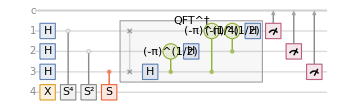

```mathematica
QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator["S"],3}]["Diagram"]
```

Show the diagram of the magic circuit:

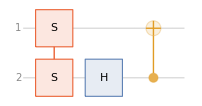

```mathematica
QuantumCircuitOperator["Magic"]["Diagram"]
```

Users should note that all of circuit diagram and its features can be customized. For more details , please refer to Diagram documentation.

Show tensor network of the magic circuit:

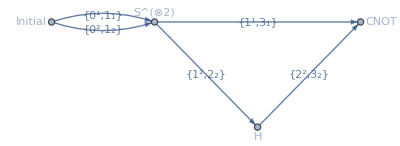

```mathematica
QuantumCircuitOperator["Magic"]["TensorNetwork",EdgeLabels->Automatic,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]
```

This TensorNetwork representation also uses indices as graph vertices with tensors as cliques:

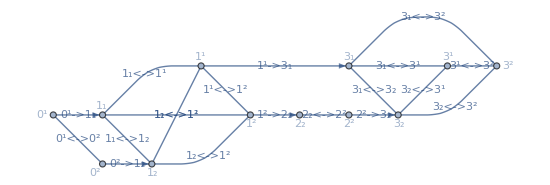

```mathematica
TensorNetworkIndexGraph[QuantumCircuitOperator["Magic"]["TensorNetwork"],EdgeLabels->Automatic,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]
```

Generate corresponding multiway graph of a circuit:

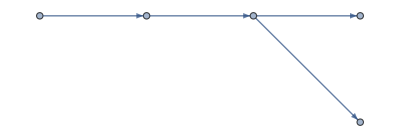

```mathematica
g=QuantumCircuitMultiwayGraph[QuantumCircuitOperator["Magic"]]
```

Add more info on edges:

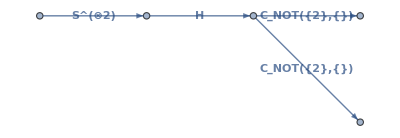

```mathematica
Graph[g,
EdgeLabels -> _ (->)^KeyValuePattern["Operator"->op_] _ :> Placed[Style[op["Label"], Bold],Center]]
```

Note that branching in the multiway graph implies the entanglement is created there.

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Quantum circuit

Quantum circuit tensor network

Quantum circuit diagram

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.